```mathematica
Get["xlr8r.m"]
```

xlr8r 0.74 (13 May 2009) loaded 13 May 2009 at 18:01 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

Original notebook 2002  (B.Shapiro)
revised 2009 for xlr8r & m7 (requires xlr8r v.074)

NOTE: Most of the larger plots have been deleted from this notebook to save space. The commands to recover those plots remain.

References: 
(1)  Gonze D & Goldbeter A (2000) A model for a network of phosphorylation-dephosphorylation cycles displaying the dynamics of dominoes and clocks, J. Theor. Biol; 210:167-186. The models in this notebook are based on this paper.
(2) Murray AW & Kirschner MW (1989) Dominoes and clocks: the union of two views of the cell cycle, Science: 246:614-621. The original concept.

## Ring Network with Hill Function Activation (e.g., Michaelis-Menten Kinetics) - similar to Gonze & Goldbeter's method

## Define the Network and illustrate a set of functions

```mathematica
xyNetwork[n_]:= Module[{dominoes},
dominoes =
Table[{{Overscript[X[i]↦Y[i], X[Mod[i+2,n]]], hill[vmax->V1, khalf-> K1]},
{Overscript[Y[i]↦X[i], X[i-1]], hill[vmax->V2, khalf-> K2]}
},{i,1,n}]  /.{X[0]-> X[n]} ;
Apply[Join,dominoes]

]
```

```mathematica
interpret[xyNetwork[4]]
```

{{X[1]'[t]==-(V1 X[1][t] X[3][t])/(K1+X[1][t])+(V2 X[4][t] Y[1][t])/(K2+Y[1][t]),X[2]'[t]==-(V1 X[2][t] X[4][t])/(K1+X[2][t])+(V2 X[1][t] Y[2][t])/(K2+Y[2][t]),X[3]'[t]==-(V1 X[1][t] X[3][t])/(K1+X[3][t])+(V2 X[2][t] Y[3][t])/(K2+Y[3][t]),X[4]'[t]==-(V1 X[2][t] X[4][t])/(K1+X[4][t])+(V2 X[3][t] Y[4][t])/(K2+Y[4][t]),Y[1]'[t]==(V1 X[1][t] X[3][t])/(K1+X[1][t])-(V2 X[4][t] Y[1][t])/(K2+Y[1][t]),Y[2]'[t]==(V1 X[2][t] X[4][t])/(K1+X[2][t])-(V2 X[1][t] Y[2][t])/(K2+Y[2][t]),Y[3]'[t]==(V1 X[1][t] X[3][t])/(K1+X[3][t])-(V2 X[2][t] Y[3][t])/(K2+Y[3][t]),Y[4]'[t]==(V1 X[2][t] X[4][t])/(K1+X[4][t])-(V2 X[3][t] Y[4][t])/(K2+Y[4][t])},{X[1],X[2],X[3],X[4],Y[1],Y[2],Y[3],Y[4]}}

## Run a 4-domino network

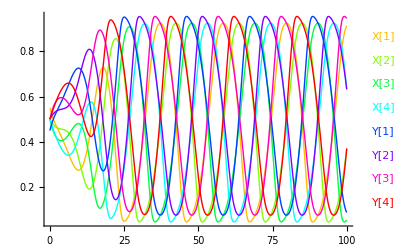

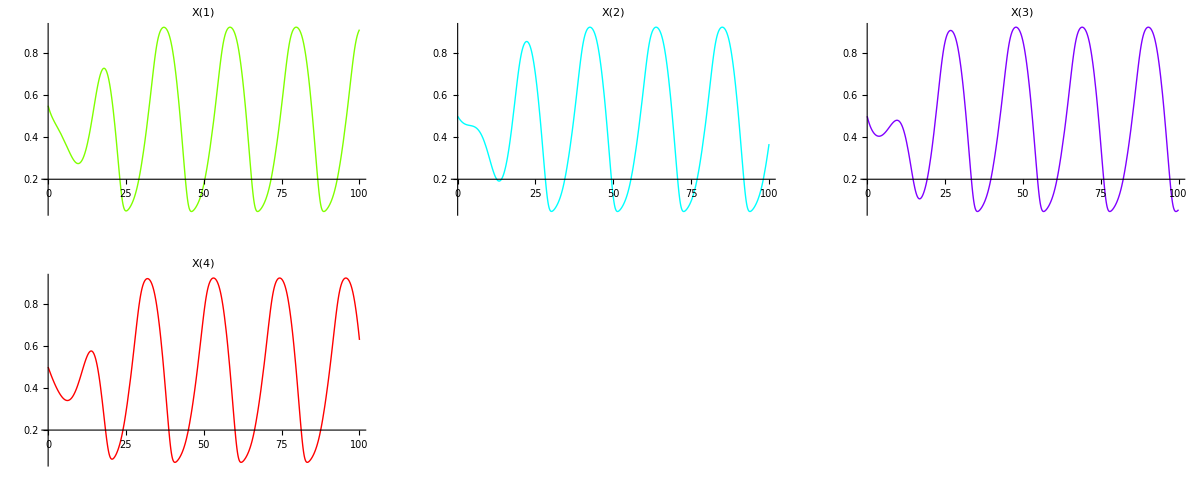

{{X[1]→InterpolatingFunction[{{0.,100.}},<>],X[2]→InterpolatingFunction[{{0.,100.}},<>],X[3]→InterpolatingFunction[{{0.,100.}},<>],X[4]→InterpolatingFunction[{{0.,100.}},<>],Y[1]→InterpolatingFunction[{{0.,100.}},<>],Y[2]→InterpolatingFunction[{{0.,100.}},<>],Y[3]→InterpolatingFunction[{{0.,100.}},<>],Y[4]→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
n=run[xyNetwork[4]/.{K1-> .1, K2->1, V1-> .5, V2-> 1},initialConditions-> {X[1][0]==0.55, X[2][0]==0.5,X[3][0]==0.5,X[4][0]==0.5, Y[1][0]==0.45, Y[2][0]==0.5,Y[3][0]==0.5,Y[4][0]==0.5 }, timeSpan-> 100, plot-> True, plotVariables-> {X[1],X[2],X[3],X[4],Y[1],Y[2],Y[3],Y[4]},gridPlotVariables-> {X[1],X[2],X[3],X[4]}]
```

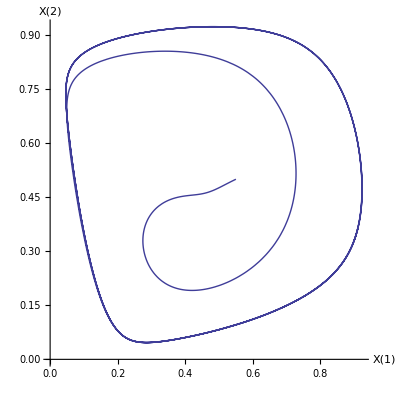

-Graphics3D-

```mathematica
ParametricPlot[Evaluate[{X[1][t],X[2][t]}/.n],{t,0,100},AxesLabel-> {X[1],X[2]}]
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.n],{t,0,100} ,PlotPoints-> 500,AxesLabel-> {X[1],X[2],X[3]}]
```

## 4-domino network with "square-wave" like activation

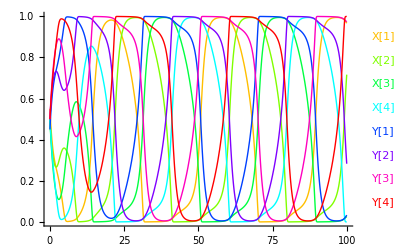

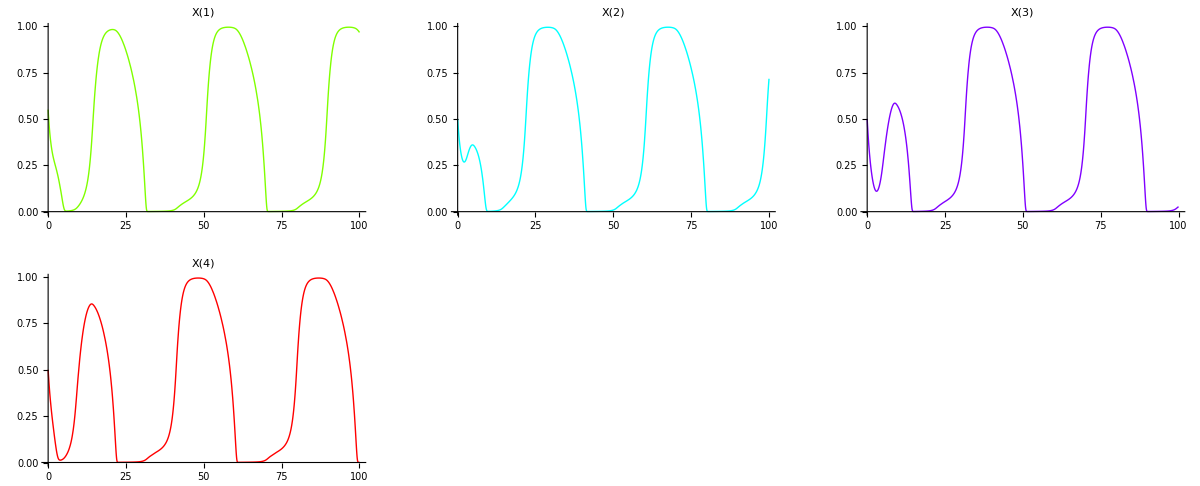

```mathematica
n=run[xyNetwork[4]/.{K1-> .05, K2->1, V1->1, V2-> 1},MaxSteps-> 25000, initialConditions-> {X[1][0]==0.55, X[2][0]==0.5,X[3][0]==0.5,X[4][0]==0.5, Y[1][0]==0.45, Y[2][0]==0.5,Y[3][0]==0.5,Y[4][0]==0.5 }, timeSpan-> 100, plot-> True, plotVariables-> {X[1],X[2],X[3],X[4],Y[1],Y[2],Y[3],Y[4]},gridPlotVariables-> {X[1],X[2],X[3],X[4]}];
```

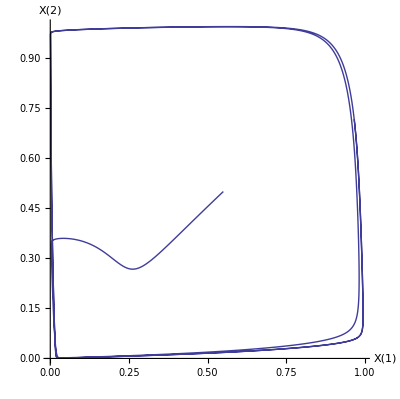

```mathematica
ParametricPlot[Evaluate[{X[1][t],X[2][t]}/.n],{t,0,100},AxesLabel-> {X[1],X[2]}, PlotPoints-> 1000]
```

```mathematica
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.n],{t,0,100} ,PlotPoints-> 500,AxesLabel-> {X[1],X[2],X[3]},PlotPoints-> 1000]
```

-Graphics3D-

## 25-domino network just for fun

```mathematica
n=run[xyNetwork[25]/.{K1->.1,K2->1,V1->1,V2->.5},initialConditions->Join[{X[1][0]==0.51},Table[X[i][0]==0.5,{i,2,25}]],timeSpan->300];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Y[1],Y[2],Y[3],Y[4],Y[5],Y[6],Y[7],Y[8],Y[9],Y[10],Y[11],Y[12],Y[13],Y[14],Y[15],Y[16],Y[17],Y[18],Y[19],Y[20],Y[21],Y[22],Y[23],Y[24],Y[25]}

```mathematica
runPlot[n, { X[1], X[2], X[3], X[4], X[5]}]
```

```mathematica
gridPlot[n, X/@Range[25], plotColumns-> 6, ImageSize-> 1000]
```

```mathematica
ParametricPlot[Evaluate[{X[1][t],X[2][t]}/.n],{t,0,300} ,PlotPoints-> 500,AxesLabel-> {X[1],X[2]}]
```

```mathematica
ParametricPlot[Evaluate[{X[1][t],Y[1][t]}/.n],{t,0,300} ,PlotPoints-> 500,AxesLabel-> {X[1],Y[1]}]
```

```mathematica
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.n],{t,0,300} ,PlotPoints-> 500,AxesLabel-> {X[1],X[2],X[3]}]
```

## Do the same thing with a mass-action kinetics (no hill functions)

## Here is the network - put a 3-item cascade in each domino

```mathematica
pnCascade[n_]:= Module[{dominoes,i},
dominoes =
Table[{Underoverscript[Z[i]⇄Y[i]⇄X[i], X[Mod[i+2,n]], X[i-1]],af,df,kf,ar,dr,kr},{i,1,n}]  /.{X[0]-> X[n]} ; 
Return[dominoes]
]
```

```mathematica
pnCascade[4]
```

{{(Z[1]⇄Y[1]⇄X[1])_X[3]^X[4],af,df,kf,ar,dr,kr},{(Z[2]⇄Y[2]⇄X[2])_X[4]^X[1],af,df,kf,ar,dr,kr},{(Z[3]⇄Y[3]⇄X[3])_X[1]^X[2],af,df,kf,ar,dr,kr},{(Z[4]⇄Y[4]⇄X[4])_X[2]^X[3],af,df,kf,ar,dr,kr}}

## 5-domino network

```mathematica
n=run[pnCascade[5]/.{af->1,df-> 0, kf->1,ar-> 1, dr->0, kr-> 1}, MaxSteps-> 25000,
initialConditions->{X[1][0]==0.55,Z[1][0]==.45,X[2][0]==0.5,Z[2][0]==0.5,X[3][0]==0.5,Z[3][0]==0.5,X[4][0]==0.5,Z[4][0]==0.5,X[5][0]==0.5, Z[5][0]==0.5}, timeSpan-> 150];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],X[4]],Bind[X[1],Y[2]],Bind[X[1],Y[4]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],X[5]],Bind[X[2],Y[3]],Bind[X[2],Y[5]],Bind[X[2],Z[3]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],Y[2]],Bind[X[4],Y[5]],Bind[X[4],Z[5]],Bind[X[5],Y[1]],Bind[X[5],Y[3]],Bind[X[5],Z[1]],Y[1],Y[2],Y[3],Y[4],Y[5]}

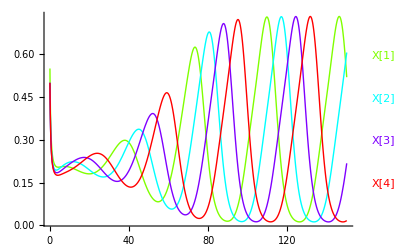

```mathematica
runPlot[n, X/@Range[4]]
```

## vary the concentrations a little - there is a little less material at stage 1 than all the other stages x[i]+y[i]+z[i]=1.5 for i>1; x[1]+y[1]+z[1]=1.25

#### shorthand run function

```mathematica
cascadeRun[n_,tmax_]:=run[pnCascade[n]/.{af->1,df-> 0, kf->1,ar-> 1, dr->0, kr-> 1}, MaxSteps-> 25000,
initialConditions-> Join[{X[1][0]==.55,Y[1][0]==0.45,Z[1][0]==0.25},
Table[X[i][0]==0.5,{i,2,n}],
Table[Y[i][0]==0.5,{i,2,n}],
Table[Z[i][0]==0.5,{i,2,n}]
],
 timeSpan-> tmax,plot-> True, plotVariables-> Table[X[i],{i,1,n}]]
```

#### 4-domino network

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],Y[2]],Bind[X[1],Y[3]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],Y[3]],Bind[X[2],Y[4]],Bind[X[2],Z[3]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],Y[1]],Bind[X[4],Y[2]],Bind[X[4],Z[1]]}

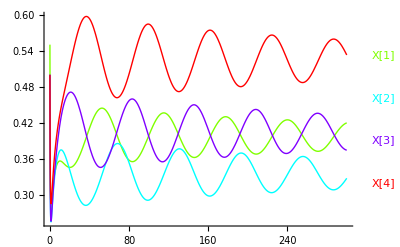

```mathematica
cascadeRun[4,300];
```

#### 5-domino network

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],X[4]],Bind[X[1],Y[2]],Bind[X[1],Y[4]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],X[5]],Bind[X[2],Y[3]],Bind[X[2],Y[5]],Bind[X[2],Z[3]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],Y[2]],Bind[X[4],Y[5]],Bind[X[4],Z[5]],Bind[X[5],Y[1]],Bind[X[5],Y[3]],Bind[X[5],Z[1]]}

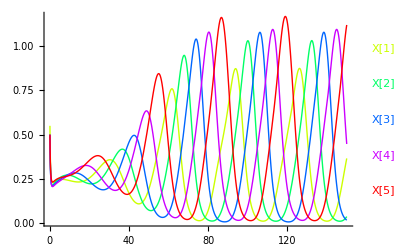

```mathematica
cascadeRun[5,150];
```

#### 10-domino network

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],X[9]],Bind[X[1],Y[2]],Bind[X[1],Y[9]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],X[10]],Bind[X[2],Y[3]],Bind[X[2],Y[10]],Bind[X[2],Z[3]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],X[6]],Bind[X[4],Y[2]],Bind[X[4],Y[5]],Bind[X[4],Z[5]],Bind[X[5],X[7]],Bind[X[5],Y[3]],Bind[X[5],Y[6]],Bind[X[5],Z[6]],Bind[X[6],X[8]],Bind[X[6],Y[4]],Bind[X[6],Y[7]],Bind[X[6],Z[7]],Bind[X[7],X[9]],Bind[X[7],Y[5]],Bind[X[7],Y[8]],Bind[X[7],Z[8]],Bind[X[8],X[10]],Bind[X[8],Y[6]],Bind[X[8],Y[9]],Bind[X[8],Z[9]],Bind[X[9],Y[7]],Bind[X[9],Y[10]],Bind[X[9],Z[10]],Bind[X[10],Y[1]],Bind[X[10],Y[8]],Bind[X[10],Z[1]]}

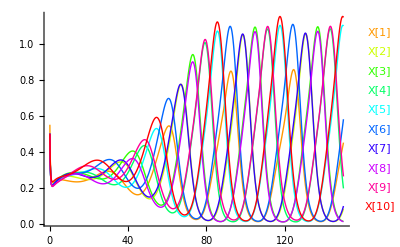

```mathematica
cascadeRun[10,150];
```

## now try it with the x[i]+y[i]+z[i]=1.5 at each stage

#### shorthand function to do run & make plots

```mathematica
cr[n_,tmax_]:=Module[{ns},

ns=run[pnCascade[n]/.{af->1,df-> 0, kf->1,ar-> 1, dr->0, kr-> 1}, MaxSteps-> 25000,
initialConditions-> Join[{X[1][0]==.55,Y[1][0]==0.45,Z[1][0]==0.5},
Table[X[i][0]==0.5,{i,2,n}],
Table[Y[i][0]==0.5,{i,2,n}],
Table[Z[i][0]==0.5,{i,2,n}]
],
plot-> True, timeSpan-> tmax,plotVariables-> Table[X[i],{i,1,n}]];
ParametricPlot[Evaluate[{X[1][t],X[2][t]}/.ns],{t,0,tmax},PlotPoints-> 1000,AxesLabel-> {X[1],X[2]}]//Print;
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.ns],{t,0,tmax},PlotPoints-> 1000,AxesLabel-> {X[1],X[2],X[3]}]//Print;

ParametricPlot3D[Evaluate[{X[1][t],Y[1][t],Z[1][t]}/.ns],{t,0,tmax},PlotPoints-> 1000,AxesLabel-> {X[1],Y[1],Z[1]}]//Print;
Return[ns];
];
```

#### 5-domino network

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],X[4]],Bind[X[1],Y[2]],Bind[X[1],Y[4]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],X[5]],Bind[X[2],Y[3]],Bind[X[2],Y[5]],Bind[X[2],Z[3]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],Y[2]],Bind[X[4],Y[5]],Bind[X[4],Z[5]],Bind[X[5],Y[1]],Bind[X[5],Y[3]],Bind[X[5],Z[1]]}

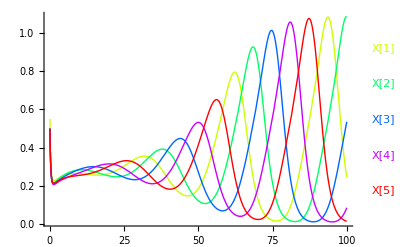

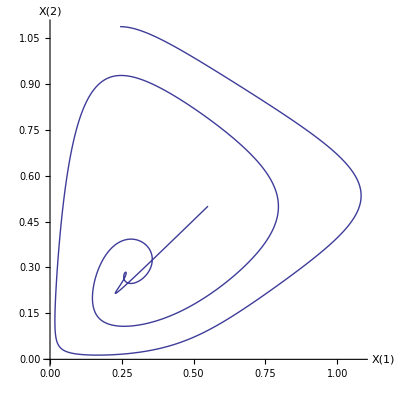

-Graphics3D-

-Graphics3D-

```mathematica
cr[5,100];
```

#### 10-domino network

```mathematica
cr[10,300];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[X[1],X[3]],Bind[X[1],X[9]],Bind[X[1],Y[2]],Bind[X[1],Y[9]],Bind[X[1],Z[2]],Bind[X[2],X[4]],Bind[X[2],X[10]],Bind[X[2],Y[3]],Bind[X[2],Y[10]],Bind[X[2],Z[3]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[3],Y[4]],Bind[X[3],Z[4]],Bind[X[4],X[6]],Bind[X[4],Y[2]],Bind[X[4],Y[5]],Bind[X[4],Z[5]],Bind[X[5],X[7]],Bind[X[5],Y[3]],Bind[X[5],Y[6]],Bind[X[5],Z[6]],Bind[X[6],X[8]],Bind[X[6],Y[4]],Bind[X[6],Y[7]],Bind[X[6],Z[7]],Bind[X[7],X[9]],Bind[X[7],Y[5]],Bind[X[7],Y[8]],Bind[X[7],Z[8]],Bind[X[8],X[10]],Bind[X[8],Y[6]],Bind[X[8],Y[9]],Bind[X[8],Z[9]],Bind[X[9],Y[7]],Bind[X[9],Y[10]],Bind[X[9],Z[10]],Bind[X[10],Y[1]],Bind[X[10],Y[8]],Bind[X[10],Z[1]]}

## Ring Network Backward coupling only

## Define the generic network

```mathematica
bwNet[n_]:= Module[{dominoes,i},
dominoes =
Table[{Underoverscript[Z[i]⇄Y[i]⇄X[i], X[Mod[i+2,n]], Enz],a,d,k,a,d,k},{i,1,n}]  /.{X[0]-> X[n]} ; 
Return[dominoes]
]
```

```mathematica
bwNet[4]
```

{{(Z[1]⇄Y[1]⇄X[1])_X[3]^Enz,a,d,k,a,d,k},{(Z[2]⇄Y[2]⇄X[2])_X[4]^Enz,a,d,k,a,d,k},{(Z[3]⇄Y[3]⇄X[3])_X[1]^Enz,a,d,k,a,d,k},{(Z[4]⇄Y[4]⇄X[4])_X[2]^Enz,a,d,k,a,d,k}}

```mathematica
ic[n_,val_]:=Flatten[ Map[{X[#][0]==val,Y[#][0]==val, Z[#][0]==val}&,Range[2,n]]];
ic[n_,val_,X1_, Y1_, Z1_]:=Join[{X[1][0]==X1, Y[1][0]==Y1,Z[1][0]==Z1},ic[n,val]]
```

```mathematica
ic[5,.5,.55,.45,.5]
```

{X[1][0]==0.55,Y[1][0]==0.45,Z[1][0]==0.5,X[2][0]==0.5,Y[2][0]==0.5,Z[2][0]==0.5,X[3][0]==0.5,Y[3][0]==0.5,Z[3][0]==0.5,X[4][0]==0.5,Y[4][0]==0.5,Z[4][0]==0.5,X[5][0]==0.5,Y[5][0]==0.5,Z[5][0]==0.5}

#### 5-domino oscillating network

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[Enz,Y[1]],Bind[Enz,Y[2]],Bind[Enz,Y[3]],Bind[Enz,Y[4]],Bind[Enz,Y[5]],Bind[Enz,Z[1]],Bind[Enz,Z[2]],Bind[Enz,Z[3]],Bind[Enz,Z[4]],Bind[Enz,Z[5]],Bind[X[1],X[3]],Bind[X[1],X[4]],Bind[X[1],Y[4]],Bind[X[2],X[4]],Bind[X[2],X[5]],Bind[X[2],Y[5]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[4],Y[2]],Bind[X[5],Y[3]]}

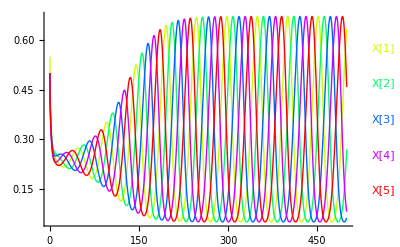

```mathematica
n=run[bwNet[5]/.{a->1, d-> 1, k-> 10}, MaxSteps-> 25000,
initialConditions->{X[1][0]==0.55,Y[1][0]==0.45,Z[1][0]==0.5,X[2][0]==0.5,Y[2][0]==0.5,Z[2][0]==0.5,X[3][0]==0.5,Y[3][0]==0.5,Z[3][0]==0.5,X[4][0]==0.5,Y[4][0]==0.5,Z[4][0]==0.5,X[5][0]==0.5,Y[5][0]==0.5,Z[5][0]==0.5,
 Enz[0]==.2},

plotVariables->(X/@Range[5]),plotColumns-> 6, plot-> True, 
timeSpan-> 500
];
```

```mathematica
gridPlot[n, plotColumns-> 6, ImageSize-> 1000]
```

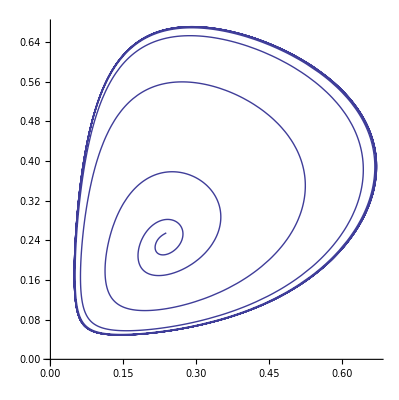

```mathematica
ParametricPlot[Evaluate[{X[1][t],X[2][t]}/.n],{t,10,500}]
```

```mathematica
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.n],{t,10,500},PlotPoints-> 500]
```

-Graphics3D-

```mathematica
ic[5,.25,.55,.45,.5]
```

{X[1][0]==0.55,Y[1][0]==0.45,Z[1][0]==0.5,X[2][0]==0.25,Y[2][0]==0.25,Z[2][0]==0.25,X[3][0]==0.25,Y[3][0]==0.25,Z[3][0]==0.25,X[4][0]==0.25,Y[4][0]==0.25,Z[4][0]==0.25,X[5][0]==0.25,Y[5][0]==0.25,Z[5][0]==0.25}

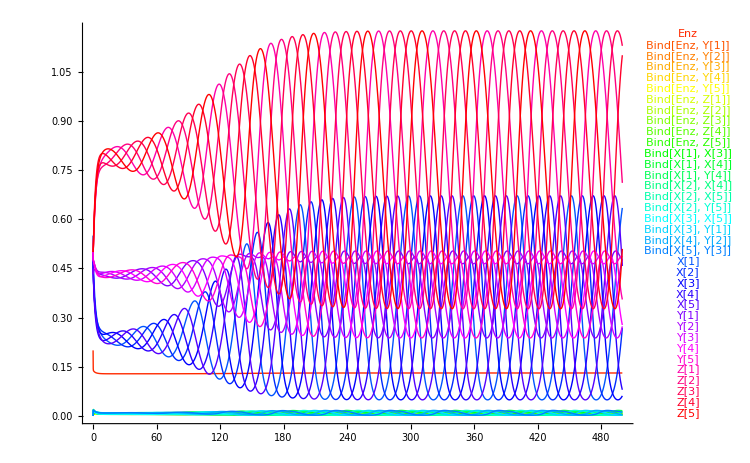

```mathematica
runPlot[n, ImageSize-> 750]
```

#### 15-domino oscillating network

```mathematica
ic2=Append[ic[25,.5,.55,.45,.5], Enz[0]==0.2]
```

{X[1][0]==0.55,Y[1][0]==0.45,Z[1][0]==0.5,X[2][0]==0.5,Y[2][0]==0.5,Z[2][0]==0.5,X[3][0]==0.5,Y[3][0]==0.5,Z[3][0]==0.5,X[4][0]==0.5,Y[4][0]==0.5,Z[4][0]==0.5,X[5][0]==0.5,Y[5][0]==0.5,Z[5][0]==0.5,X[6][0]==0.5,Y[6][0]==0.5,Z[6][0]==0.5,X[7][0]==0.5,Y[7][0]==0.5,Z[7][0]==0.5,X[8][0]==0.5,Y[8][0]==0.5,Z[8][0]==0.5,X[9][0]==0.5,Y[9][0]==0.5,Z[9][0]==0.5,X[10][0]==0.5,Y[10][0]==0.5,Z[10][0]==0.5,X[11][0]==0.5,Y[11][0]==0.5,Z[11][0]==0.5,X[12][0]==0.5,Y[12][0]==0.5,Z[12][0]==0.5,X[13][0]==0.5,Y[13][0]==0.5,Z[13][0]==0.5,X[14][0]==0.5,Y[14][0]==0.5,Z[14][0]==0.5,X[15][0]==0.5,Y[15][0]==0.5,Z[15][0]==0.5,X[16][0]==0.5,Y[16][0]==0.5,Z[16][0]==0.5,X[17][0]==0.5,Y[17][0]==0.5,Z[17][0]==0.5,X[18][0]==0.5,Y[18][0]==0.5,Z[18][0]==0.5,X[19][0]==0.5,Y[19][0]==0.5,Z[19][0]==0.5,X[20][0]==0.5,Y[20][0]==0.5,Z[20][0]==0.5,X[21][0]==0.5,Y[21][0]==0.5,Z[21][0]==0.5,X[22][0]==0.5,Y[22][0]==0.5,Z[22][0]==0.5,X[23][0]==0.5,Y[23][0]==0.5,Z[23][0]==0.5,X[24][0]==0.5,Y[24][0]==0.5,Z[24][0]==0.5,X[25][0]==0.5,Y[25][0]==0.5,Z[25][0]==0.5,Enz[0]==0.2}

```mathematica
n=run[bwNet[25]/.{a->1, d-> 1, k-> 10}, initialConditions-> ic2, timeSpan-> 1000
];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[Enz,Y[1]],Bind[Enz,Y[2]],Bind[Enz,Y[3]],Bind[Enz,Y[4]],Bind[Enz,Y[5]],Bind[Enz,Y[6]],Bind[Enz,Y[7]],Bind[Enz,Y[8]],Bind[Enz,Y[9]],Bind[Enz,Y[10]],Bind[Enz,Y[11]],Bind[Enz,Y[12]],Bind[Enz,Y[13]],Bind[Enz,Y[14]],Bind[Enz,Y[15]],Bind[Enz,Y[16]],Bind[Enz,Y[17]],Bind[Enz,Y[18]],Bind[Enz,Y[19]],Bind[Enz,Y[20]],Bind[Enz,Y[21]],Bind[Enz,Y[22]],Bind[Enz,Y[23]],Bind[Enz,Y[24]],Bind[Enz,Y[25]],Bind[Enz,Z[1]],Bind[Enz,Z[2]],Bind[Enz,Z[3]],Bind[Enz,Z[4]],Bind[Enz,Z[5]],Bind[Enz,Z[6]],Bind[Enz,Z[7]],Bind[Enz,Z[8]],Bind[Enz,Z[9]],Bind[Enz,Z[10]],Bind[Enz,Z[11]],Bind[Enz,Z[12]],Bind[Enz,Z[13]],Bind[Enz,Z[14]],Bind[Enz,Z[15]],Bind[Enz,Z[16]],Bind[Enz,Z[17]],Bind[Enz,Z[18]],Bind[Enz,Z[19]],Bind[Enz,Z[20]],Bind[Enz,Z[21]],Bind[Enz,Z[22]],Bind[Enz,Z[23]],Bind[Enz,Z[24]],Bind[Enz,Z[25]],Bind[X[1],X[3]],Bind[X[1],X[24]],Bind[X[1],Y[24]],Bind[X[2],X[4]],Bind[X[2],X[25]],Bind[X[2],Y[25]],Bind[X[3],X[5]],Bind[X[3],Y[1]],Bind[X[4],X[6]],Bind[X[4],Y[2]],Bind[X[5],X[7]],Bind[X[5],Y[3]],Bind[X[6],X[8]],Bind[X[6],Y[4]],Bind[X[7],X[9]],Bind[X[7],Y[5]],Bind[X[8],X[10]],Bind[X[8],Y[6]],Bind[X[9],X[11]],Bind[X[9],Y[7]],Bind[X[10],X[12]],Bind[X[10],Y[8]],Bind[X[11],X[13]],Bind[X[11],Y[9]],Bind[X[12],X[14]],Bind[X[12],Y[10]],Bind[X[13],X[15]],Bind[X[13],Y[11]],Bind[X[14],X[16]],Bind[X[14],Y[12]],Bind[X[15],X[17]],Bind[X[15],Y[13]],Bind[X[16],X[18]],Bind[X[16],Y[14]],Bind[X[17],X[19]],Bind[X[17],Y[15]],Bind[X[18],X[20]],Bind[X[18],Y[16]],Bind[X[19],X[21]],Bind[X[19],Y[17]],Bind[X[20],X[22]],Bind[X[20],Y[18]],Bind[X[21],X[23]],Bind[X[21],Y[19]],Bind[X[22],X[24]],Bind[X[22],Y[20]],Bind[X[23],X[25]],Bind[X[23],Y[21]],Bind[X[24],Y[22]],Bind[X[25],Y[23]]}

```mathematica
runPlot[n, X/@Range[5]]
```

```mathematica
gridPlot[n, plotColumns-> 12, ImageSize-> 1000]
```

```mathematica
ParametricPlot[Evaluate[{X[2][t],X[3][t]}/.n],{t,3,1000}]
```

```mathematica
ParametricPlot3D[Evaluate[{X[1][t],X[2][t],X[3][t]}/.n],{t,0,1000},PlotPoints-> 1000]
```

```mathematica
ParametricPlot3D[Evaluate[{X[1][t],Y[1][t],Z[1][t]}/.n],{t,0,1000},PlotPoints-> 1000,AxesLabel-> {X,Y,Z}]
```

```mathematica
ParametricPlot[Evaluate[{X[1][t],Y[1][t]}/.n],{t,0,1000},PlotPoints-> 1000,AxesLabel-> {X,Y}]
```

```mathematica
ParametricPlot[Evaluate[{Y[1][t],Z[1][t]}/.n],{t,0,1000},PlotPoints-> 1000,AxesLabel-> {Y,Z}]
```

```mathematica
runPlot[n, Y/@Range[15]]
```

```mathematica
runPlot[n, Z/@Range[15], { 0, 500}]
```

```mathematica
Plot[Evaluate[Enz[t]/.n],{t,0,500}, PlotPoints-> 1000]
```